Practical 7

Plotting the characteristic for first order PDE
1. yu_x - xu_y= 0
The characteristic system is given by dx/y = dy/x = du/0 and the characteristic equations are given by x^2+ y^2 = c1  and u = c2. Taking c1 = 1 and 3 and c2 = 3 and 8.

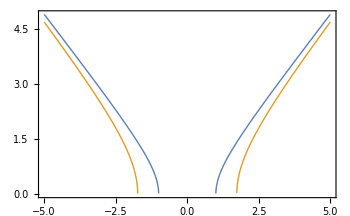

```mathematica
Plot[{Sqrt[x^2 - 1], Sqrt[x^2 - 3]}, {x, -5, 5}, PlotStyle -> Thick, Frame -> True]
```

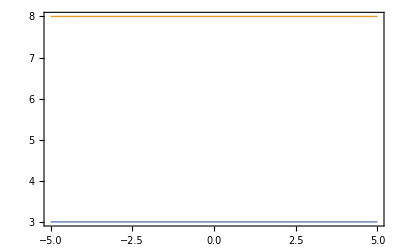

```mathematica
Plot[{3, 8}, {x, -5, 5}, PlotStyle -> Thick, Frame-> True]
```

2.  xu_x + yu_y = u
The characteristic system is given by dx/x = dy/y = du/u and the characteristic equations are given by y/x = c1 and u/x = c2. Taking c1 = 1 and 3 and c2 = 3 and 8.

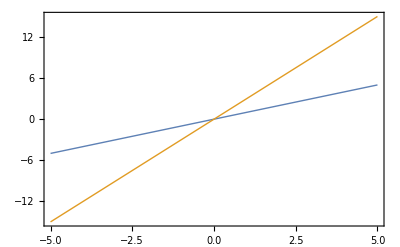

```mathematica
Plot[{x, 3x}, {x, -5, 5}, PlotStyle -> Thick, Frame -> True]
```

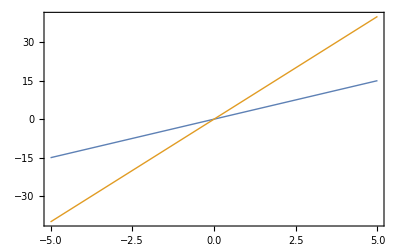

```mathematica
Plot[{3x, 8x}, {x, -5, 5}, PlotStyle -> Thick, Frame -> True]
```

3.    (y + xu)u_x - (x + uy )u_y= x^2 - y^2
The characteristic system is given by dx/(y + ux)= dy/(-(x + uy))= du/(x^2-y^2) and the characteristic equations are given by xy + u = c1 and x^2 + y^2 - u^2 = c2. Taking c1 = 0and 9 and c2 = 0 and 10.

```mathematica
Plot3D[{-x*y, -x*y+9},{x, -5, 5}, {y, -5, 5}, PlotStyle -> Thick]
```

-Graphics3D-

```mathematica
Plot3D[{Sqrt[x^2+y^2], Sqrt[x^2+y^2 - 10]}, {x, -5, 5}, {y, -10, 10}, PlotStyle-> Thick]
```

-Graphics3D-

Questions
1. xu_x - yu_y= u
2. y^2 u_x - xyu_y= x(u - 2y)
3. u(x+y) u_x - u(x - y)u_y=  x^2+ y^2 
4. u_x - u_y= 1

1.

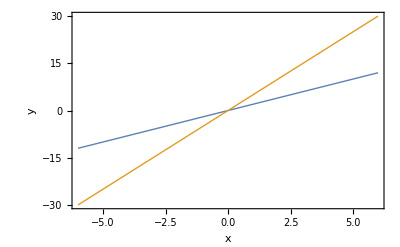

```mathematica
Plot[{2x,5x},{x,-6,6},PlotStyle->Thick,Frame->True,AxesLabel->{"x","y"}]
```

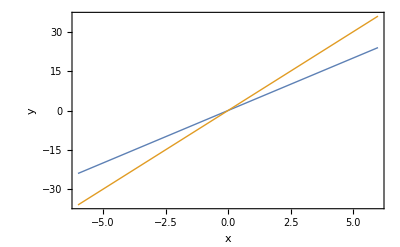

```mathematica
Plot[{4x,6x},{x,-6,6},PlotStyle->Thick,Frame->True,AxesLabel->{"x","y"}]
```

2.

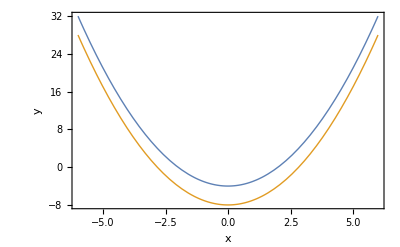

```mathematica
Plot[{x^2-4,x^2-8},{x,-6,6},PlotStyle->Thick,Frame->True,AxesLabel->{"x","y"}]
```

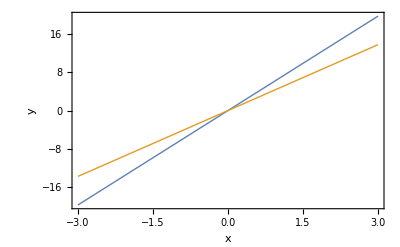

```mathematica
Plot[{y(8-2*Log[2]),y(6-2*Log[2])},{y,-3,3},PlotStyle->Thick,Frame->True,AxesLabel->{"x","y"}]
```

3.

```mathematica
Plot3D[{(x^2-y^2-1)/2,(x^2-y^2-2)/2},{x,-6,6},{y,-6,6},PlotStyle->Thick]
```

-Graphics3D-

```mathematica
Plot3D[{Sqrt[x^2-y^2],Sqrt[x^2-y^2+2]},{x,-5,5},{y,-10,10},PlotStyle->Thick]
```

-Graphics3D-

4.

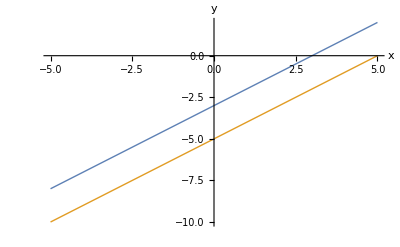

```mathematica
Plot[{x-3,x-5},{x,-5,5},PlotStyle->Thick,AxesLabel->{"x","y"}]
```

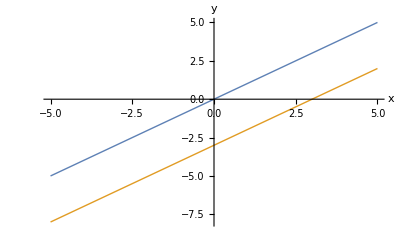

```mathematica
Plot[{y-0,y-3},{y,-5,5},PlotStyle->Thick,AxesLabel->{"x","y"}]
```